# Oscillation modes of neutron stars

Copyright 2018, Bianca de A. M. da Silva, Universidade Federal Fluminense.
Github: https://github.com/biancamendes

## EOSs

```mathematica
c=2.99792458*^10;(*cgs*)
G=6.67408*^-8;(*cgs*)
MSun=1.9884754153381435*^33 ;(*cgs*)
ρ0=2.7*^14;(*cgs; gauge density*)

table={{SLy,34.384,3.005,2.988,2.851,0.0020},
		{BBB2,34.331,3.418,2.835,2.832,0.0055},
		{ENG,34.437,3.514,3.130,3.168,0.015},
		{MPA1,34.495,3.446,3.572,2.887,0.0081}, 
		{MS1,34.858,3.224,3.033,1.325,0.019},
		{MS1b,34.855,3.456,3.011,1.425,0.015},
		{GNH3,34.648,2.664,2.194,2.304,0.0045},
		{H4,34.669,2.909,2.246,2.144,0.0028},
		{ALF2,34.616,4.070,2.411,1.890,0.043},
		{ALF4,34.314,3.009,3.438,1.803,0.023}};
```

## Parameters

```mathematica
DefEOS[EOSname_]:=Module[{EOS},

EOS=Cases[table,x_/;x[[1]]==EOSname]⟦1⟧;

p1=10^EOS⟦2⟧;
Γ1=EOS⟦3⟧;
Γ2=EOS⟦4⟧;
Γ3=EOS⟦5⟧;

ρi={2.44034*^07,3.78358*^11,2.62780*^12}/ρ0;
Γi={1.58425,1.28733,0.62223,1.35692}; 
Ki={6.80110*^-09,1.06186*^-06,5.32697*^+01,3.99874*^-08}*ρ0^(Γi-1); 

ρ1=10^14.7/ρ0;
ρ2=10^15.0/ρ0;
p1a=p1/(ρ0*c^2);
ρcr=(p1a/(Ki⟦4⟧*ρ1^Γ1))^(1/(Γi⟦4⟧-Γ1));

ρlist=Flatten[{ρi,ρcr,ρ1,ρ2,10^18}];
Γlist=Flatten[{Γi,Γ1,Γ2,Γ3}];
Klist=Flatten[{Ki,p1a/ρ1^Γ1,p1a/ρ1^Γ2,p1a*((ρ2/ρ1)^Γ2)/ρ2^Γ3}];
plist[ρ_]:=Klist*ρ^Γlist;

X[ρ_]:=Position[ρlist-ρ,First@Cases[ρlist-ρ,x_/;x>0]]⟦1,1⟧;

a[1]=0;
a[i_]:=((1+a[i-1])*ρlist⟦i-1⟧+Klist⟦i-1⟧/(Γlist⟦i-1⟧-1)*ρlist⟦i-1⟧^Γlist⟦i-1⟧)/ρlist⟦i-1⟧-1-Klist⟦i⟧/(Γlist⟦i⟧-1)*ρlist⟦i-1⟧^(Γlist⟦i⟧-1);
alist= Flatten[{1+a[1],1+a[2],1+a[3],1+a[4],1+a[5],1+a[6],1+a[7]}];

alistB[n_?NumberQ]:=alist⟦Round@n⟧;
ΓlistB[n_?NumberQ]:=Γlist⟦Round@n⟧;
KlistB[n_?NumberQ]:=Klist⟦Round@n⟧;
ρlistB[n_?NumberQ]:=Flatten[{10^-14,ρlist}]⟦Round@n⟧;]
```

### Dimensionless Variables

```mathematica
aρ[r]== ρ[r]/ρ0;
ae[r]== (ρ[r]+(k*ρ[r]^Γ)/(Γ-1))*1/(ρ0*c^2);
ap[r]== (k*ρ[r]^Γ)/(ρ0*c^2);
am[r]== m[r]*Sqrt[G^3*ρ0]/c^3;
ar[r]== r*Sqrt[G*ρ0]/c;
```

## TOV Equations

```mathematica
TOV[ρc_,EOS_]:=Module[{},DefEOS[EOS];Clear[R,M,cte];rtr={};
sol=NDSolve[{m'[r]== 4*Pi*r^2*(ρ[r]*alistB[n[r]]+(KlistB[n[r]]*ρ[r]^ΓlistB[n[r]])/(ΓlistB[n[r]]-1)), ϕ'[r]== (4*Pi*KlistB[n[r]]*(ρ[r])^ΓlistB[n[r]]*r^3+m[r])/(r*(r-2*m[r])), ρ'[r]== -((ρ[r]*alistB[n[r]]+(KlistB[n[r]]*ρ[r]^ΓlistB[n[r]])/(ΓlistB[n[r]]-1)+KlistB[n[r]]*ρ[r]^ΓlistB[n[r]])/(KlistB[n[r]]*ΓlistB[n[r]]*ρ[r]^(ΓlistB[n[r]]-1)))*ϕ'[r],m[10^-15]==0,ϕ[10^-15]== 1,ρ[10^-15]==ρc,n[10^-15]==X[ρc], WhenEvent[Re[ρ[r]]==ρlistB[n[r]]&&n[r]>1,rtr=Flatten[{rtr,r}]; n[r]->n[r]-1],WhenEvent[Re[ρ[r]]==1*^-15,R=r; M=Re[m[r]]; cte=(1/2)*Log[1-2*m[r]/r]-ϕ[r]; "StopIntegration"]},{m,ϕ,ρ,n},{r,10^-15,2},DiscreteVariables->n, AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25]];

 nsol[r_]:=Re[n[r]]/.sol⟦1⟧;
 msol[r_]:=Re[m[r]]/.sol⟦1⟧;
ϕsol[r_]:=Re[ϕ[r]]/.sol⟦1⟧;
ρsol[r_]:=Re[ρ[r]]/.sol⟦1⟧;
psol[r_]:=KlistB[nsol[r]]*(ρsol[r])^ΓlistB[nsol[r]];

ϵsol[r_]:=ρsol[r]*alistB[nsol[r]]+psol[r]/(ΓlistB[nsol[r]]-1);
Γsol[r_]:=ΓlistB[nsol[r]];
```

### Plots

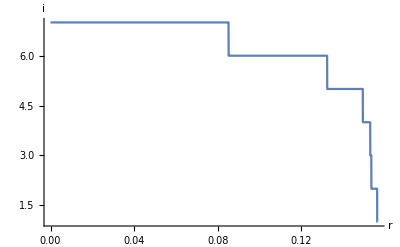

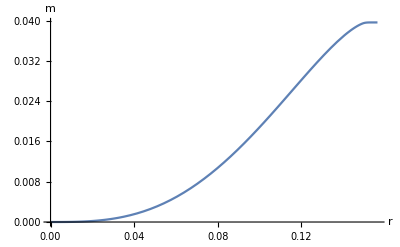

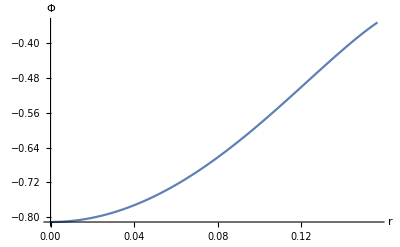

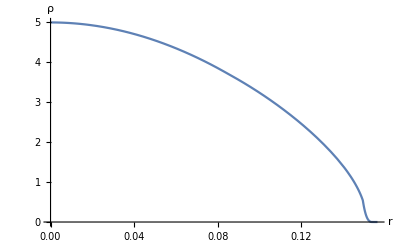

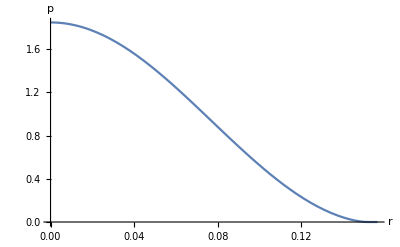

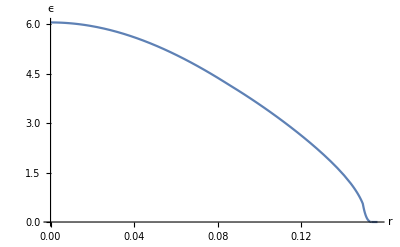

```mathematica
TOV[5,SLy]; (*example*)

Plot[nsol[r],{r,0,R},PlotRange->All,AxesLabel->{r,i}]
Plot[msol[r],{r,0,R},AxesLabel->{r,m}]
Plot[ϕsol[r]+cte,{r,0,R},AxesLabel->{r,Φ}]
Plot[ρsol[r],{r,0,R},AxesLabel->{r,ρ}]
Plot[psol[r],{r,0,R},AxesLabel->{r,p}]
Plot[ϵsol[r],{r,0,R},AxesLabel->{r,ϵ}]
```

### Mass x Radius

```mathematica
Clear[lst];
Do[
lst[i]={}; 
Do[TOV[x,table⟦i⟧⟦1⟧];lst[i]=Append[lst[i],{x,R/(Sqrt[G*ρ0]/c)/1*^5,M/(Sqrt[G^3*ρ0]/c^3)/MSun}];,{x,1.5,10,0.25}];
,{i,1,Length@table}]
```

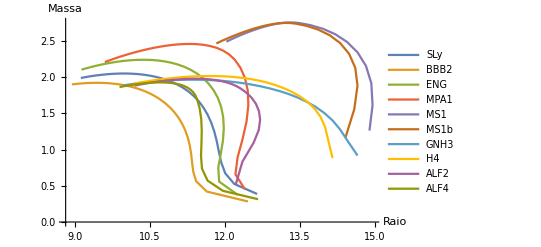

```mathematica
ListPlot[Table[lst[i]⟦All,{2,3}⟧,{i,1,Length[table]}],AxesLabel->{Raio,Massa},Joined->True,PlotLegends->Table[table⟦i⟧⟦1⟧,{i,Length[table]}]]
```

```mathematica
maximos={};
Do[maximos = Append[maximos,{lst[i]⟦Position[lst[i]⟦All,3⟧,Max[Re[lst[i]⟦All,3⟧]]]⟦1⟧⟦1⟧,2⟧,Max[Re[lst[i]⟦All,3⟧]]}], {i,1,Length@table}];
MatrixForm[maximos]
```

(9.94859 | 2.04838
9.38952 | 1.91989
10.4139 | 2.23782
11.2946 | 2.45644
13.2985 | 2.75278
13.218 | 2.7463
11.3453 | 1.96321
11.6965 | 2.01389
11.4254 | 1.97641
10.692 | 1.92553)

## Perturbation

```mathematica
Perturb[σ_?NumberQ]:=Module[{δ=10^-10},
Clear[solint,solext];solint=NDSolve[{ζ''[r]+(msol[r]/(r^2*(1-2*msol[r]/r))*(1-ϵsol[r]/psol[r])-2/r+(8*Pi*r*psol[r])/(1-2*msol[r]/r))*ζ'[r]+(1+ϵsol[r]/psol[r])/Γsol[r]*((((2*msol[r])/(r^2*(1-2*msol[r]/r))+(8*Pi*r*psol[r])/(1-2*msol[r]/r))^2)/4+(4*msol[r])/(r^3*(1-2*msol[r]/r))+(8*Pi*psol[r])/(1-2*msol[r]/r)+σ^2*(1-2*msol[r]/r)^-1/Exp[2*(ϕsol[r]+Re[cte])])*ζ[r]== 0, ζ[10^-8]==10^-24,ζ'[10^-8]== 3*10^-16,WhenEvent[Evaluate@Table[r==N@rtr⟦k⟧,{k,1,Length@rtr}], ζ'[r]->ζ'[r]*Γsol[r-δ]/Γsol[r+δ]]},ζ,{r,10^-8,R/2}, AccuracyGoal->13,PrecisionGoal->13,WorkingPrecision->24,MaxSteps->100000];
solext=NDSolve[{ζ''[r]+(msol[r]/(r^2*(1-2*msol[r]/r))*(1-ϵsol[r]/psol[r])-2/r+(8*Pi*r*psol[r])/(1-2*msol[r]/r))*ζ'[r]+(1+ϵsol[r]/psol[r])/Γsol[r]*((((2*msol[r])/(r^2*(1-2*msol[r]/r))+(8*Pi*r*psol[r])/(1-2*msol[r]/r))^2)/4+(4*msol[r])/(r^3*(1-2*msol[r]/r))+(8*Pi*psol[r])/(1-2*msol[r]/r)+σ^2*(1-2*msol[r]/r)^-1/Exp[2*(ϕsol[r]+Re[cte])])*ζ[r]== 0, ζ[R]==1,ζ'[R]==Re[1/Γsol[R]*(4/R+M/(R*(R-2*M))+σ^2/(1-2*M/R)*R^2/M)],WhenEvent[Evaluate@Table[r==N@rtr⟦k⟧,{k,1,Length@rtr}],ζ'[r]->ζ'[r]*Γsol[r+δ]/Γsol[r-δ]]},ζ,{r,R,R/2}, AccuracyGoal->13,PrecisionGoal->13,WorkingPrecision->24,MaxSteps->100000];

((ζ'[R/2]/ζ[R/2])/.solint⟦1⟧)-((ζ'[R/2]/ζ[R/2])/.solext⟦1⟧)]
```

### Plots

{{2.,13.20393256457255224},{2.5,9.789645209783505104},{3.,4.911641468253111945},{3.5,-2.270539298883641802},{4.,-13.63709664296049393},{4.5,-34.40042666980396294},{5.,-86.332137298147013832},{5.5,-528.53458410375310589},{6.,215.79496920661509618},{6.5,102.63286311451963629},{7.,69.761214825139865196},{7.5,52.461430413841904109},{8.,40.553888733706797071},{8.5,30.88723587704149679},{9.,22.100644440680067768},{9.5,13.43093794702693793},{10.,4.314165009803072544},{10.5,-5.81216606035197357},{11.,-17.68779769617262435},{11.5,-32.529675899023160176},{12.,-52.777090883813243235},{12.5,-84.581150115956895145},{13.,-150.29261328379521306},{13.5,-455.46269462436268009},{14.,387.0427096213050948},{14.5,102.7003606664770545},{15.,32.73051582962740683},{15.5,-8.630932145388220481},{16.,-43.999703252190784013},{16.5,-81.881020497665061637},{17.,-129.954588585194594079}}

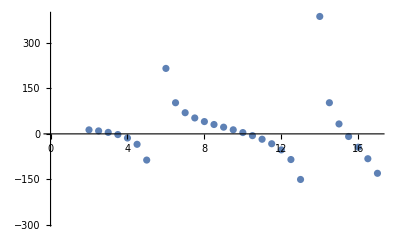

```mathematica
TOV[5,SLy]; (*example*)

Off[NDSolve::precw]
Table[{sigma,Perturb[sigma ]},{sigma,2,17,0.5}] 
ListPlot[%]
```

```mathematica
FindRoot[Perturb[σ ],{σ,3,3.5}]
FindRoot[Perturb[σ ],{σ,10,10.5}]
FindRoot[Perturb[σ ],{σ,15,15.5}]
```

{σ→3.36325}

{σ→10.221}

{σ→15.3841}

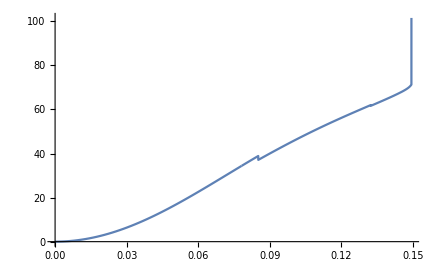

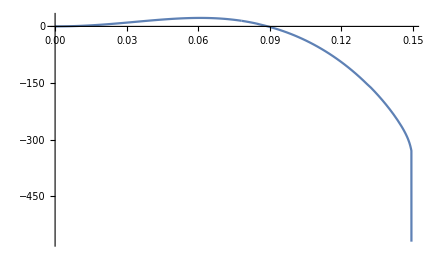

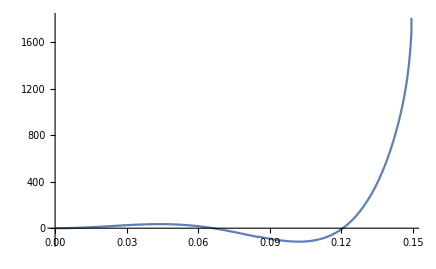

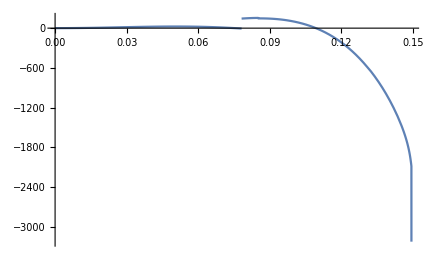

```mathematica
Perturb[3.3632462948142345];
grafn0=Show[Plot[(ζ'[r]/.solint)/(ζ[R/2]/.solint),{r,0,R/2}],Plot[(ζ'[r]/.solext)/(ζ[R/2]/.solext),{r,R/2,R}],PlotRange->All]
Perturb[10.221009781355878];
grafn1=Show[Plot[(ζ'[r]/.solint)/(ζ[R/2]/.solint),{r,0,R/2}],Plot[(ζ'[r]/.solext)/(ζ[R/2]/.solext),{r,R/2,R}],PlotRange->All]
Perturb[15.38408064767609];
grafn2=Show[Plot[(ζ'[r]/.solint)/(ζ[R/2]/.solint),{r,0,R/2}],Plot[(ζ'[r]/.solext)/(ζ[R/2]/.solext),{r,R/2,R}],PlotRange->All]
Perturb[13.00];
grafn2=Show[Plot[(ζ'[r]/.solint)/(ζ[R/2]/.solint),{r,0,R/2}],Plot[(ζ'[r]/.solext)/(ζ[R/2]/.solext),{r,R/2,R}],PlotRange->All]
```

## Characteristic Frequencies

```mathematica
flist={{"EOS","ρc","R","M","σ","n"}};
Dynamic[MatrixForm[flist]]
Do[Do[
EOS=table⟦i⟧⟦1⟧;
TOV[ρc,EOS];
j=0.1;
nn=0;
sσ1=Sign[Perturb[j]];
If[sσ1<0,α=0;While[α==0,j=j+If[ρc≤2.25,0.2,0.5]; sσ2=Sign[Perturb[j I]];If[(sσ1<sσ2),root=σ/.FindRoot[Perturb[σ I],{σ,j-If[ρc≤2.25,0.2,0.5],j}]; flist=Append[flist,{EOS, ρc,R,M,root I,0}];α=1]; sσ1=sσ2];j=0.1;sσ1=Sign[Perturb[j]]]; 
While[nn<2,j=j+If[ρc≤2.25,0.2,0.5]; sσ2=Sign[Perturb[j]];If[(sσ1>sσ2),root=σ/.FindRoot[Perturb[σ],{σ,j-If[ρc≤2.25,0.2,0.5],j}]; Perturb[root];tb=Join[Table[{r,(ζ[r]/.solint⟦1⟧)/(ζ[R/2]/.solint⟦1⟧)},{r,1.*^-5,R/2,R/50}],Table[{r,(ζ[r]/.solext⟦1⟧)/(ζ[R/2]/.solext⟦1⟧)},{r,R/2,R,R/50.}]];nn=0; Do[If[Sign[tb⟦k,2⟧]≠ Sign[tb⟦k+1,2⟧],nn=nn+1],{k,50}] ;If[nn≤2,flist=Append[flist,{EOS, ρc,R,M,root,nn}]]]; sσ1=sσ2],{ρc,1.5,10,0.25}],{i,1,Length[table]}]
Print["Tempo de processamento → ",IntegerPart[TimeUsed[]/60^2],":",IntegerPart[(TimeUsed[]-IntegerPart[TimeUsed[]/60^2]*60^2)/60],":",TimeUsed[]-IntegerPart[(TimeUsed[]-IntegerPart[TimeUsed[]/60^2]*60^2)/60]*60-IntegerPart[TimeUsed[]/60^2]*60^2]
Export["finallist.dat",flist]
```